# Tips for Fast and Efficient WL Code

## Ian Johnson Wolfram Summer School 2017

## Paradigms in Mathematica

Functional

Fastest generally paradigm

```mathematica
ClearAll[f]
```

```mathematica
f/@Range[10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
f@@@RandomReal[1,{2,2}]
```

{f[0.837799,0.196541],f[0.460766,0.941292]}

Symbolic

For some inputs, can be almost instantaneous, however can also be much much slower

```mathematica
2^80000000
```

449902592379675381092872615006620309456978610138909714306858285797649088171792408224670913637602510116561591841892547050816068560212739799728267572786558587109376
 |  |  |  |

```mathematica
2.^80000000
```

4.4990259238×10^24082399

```mathematica
Sum
```

Procedural

Can be fast, but generally will be slower than Functional

Object oriented

Generally slowest, depending on what specific operation

## Pattern based speedups

When evaluating code, attempting to “shield” evaluation using the pattern matching system can be quite useful

```mathematica
failFunc[smallThing_,otherSmallThing_]:=Graphics[{smallThing,otherSmallThing}]
```

```mathematica
failFunc[Range[1000],Range[45]]
```

-Graphics-

Instead use pattern matching to only evaluate on inputs that don’t “blow up”

```mathematica
workFunc[smallThing_Disk,otherSmallThing_Rectangle]:=Graphics[{smallThing,otherSmallThing}]
```

```mathematica
workFunc[any___]:=$Failed
```

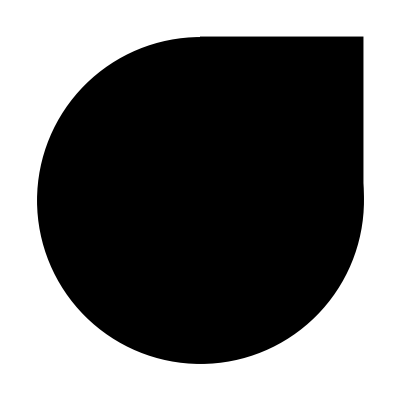

```mathematica
workFunc[Disk[],Rectangle[]]
```

```mathematica
workFunc[Range[1000],Range[45]]
```

$Failed

## Functional vs Procedural

Helper function to time the results

```mathematica
SetAttributes[time,HoldAllComplete];
time[any___]:=First[AbsoluteTiming@any];
```

```mathematica
data=Range[10^7];
```

```mathematica
Unset[$HistoryLength]
```

```mathematica
time@Total[#^2&/@data]
```

1.92155

```mathematica
time[Plus@@(#^2&/@data)]
```

1.73921

```mathematica
time@Sum[i^2,{i,1,10^7}]
```

0.005306

When performing loops, Do is faster than For, but still slow in WL

```mathematica
time[total=0;For[i=0,i≤Length[data],i++,total+=data[[i]]^2]]
```

20.7096

```mathematica
time[total=0;Do[total+=data[[i]]^2,{i,Length[data]}]]
```

9.98879

Not using indexes is still fastest:

```mathematica
time[total=0;Do[total+=i^2,{i,data}]]
```

6.35785

```mathematica
Range[5]
```

{1,2,3,4,5}

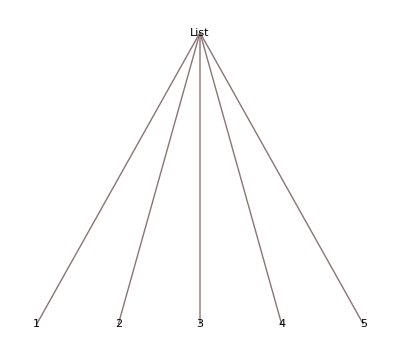

```mathematica
TreeForm[{1,2,3,4,5}]
```

#### Big picture here : Don’t use indices and don’t use For

## Vectorization

If we look back at our program that was the sum of the squares, we can speed up faster still :

```mathematica
time@Total[Power[data,2]]
```

1.53866

This is because Power is listable. Many numeric functions have the listable attribute which allows them to work faster on all of the inputs rather than go back and forth in the evaluator with Map

Sin for example is another listable function:

```mathematica
Out[325]
```

2

```mathematica
ClearSystemCache[]
```

```mathematica
Internal`Restart[]
```

```mathematica
ClearAll[data]
```

```mathematica
numericdata=N[Take[data,1000]];
```

```mathematica
Out[331]
```

```mathematica
$HistoryLength=0
```

0

```mathematica
numericdata//Short
```

{1.,2.,«9999996»,1.×10^7,1.×10^7}

```mathematica
time[Sin/@numericdata]
```

1.11805

```mathematica
time[Sin[numericdata]]
```

0.036353

```mathematica
%%/%
```

30.7554

## PackedArrays

What’s different about the two inputs:

```mathematica
Union[Head/@data]
```

{Integer}

```mathematica
time@Total[Power[Prepend[data,0],2]]
time@Total[Power[Prepend[data,0.],2]]
```

1.58059

4.96064

The difference is that the first is a packed array and the second isn’t:

```mathematica
Developer`PackedArrayQ[Prepend[data,0]]
Developer`PackedArrayQ[Prepend[data,0.]]
```

True

False

A packed array is an internal representation of a list of the same type that can be worked on faster than a list of differing types

What’s a packed array? Basically a tensor that has multiple types stored inside it. Many generative functions return packed arrays

```mathematica
Developer`PackedArrayQ[Range[10]]
```

True

Functions with listable attributes typically don’t unpack when called with the list argument:

```mathematica
Developer`PackedArrayQ[#^2&/@Range[10]]
```

False

```mathematica
Function[{num},num^2,Listable]@Range[10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Developer`PackedArrayQ[Function[{num},num,Listable]@Range[10]]
```

False

```mathematica
square[num_]:=num^2
```

```mathematica
Developer`PackedArrayQ[square@Range[10]]
```

False

```mathematica
SetAttributes[square,Listable]
```

```mathematica
FullForm[Hold[Range[10]^2]]
```

Hold[Power[Range[10],2]]

```mathematica
Developer`PackedArrayQ[Power[Range[10],2]]
```

True

Packed arrays can be Reals too, so long as it’s entirely Reals:

```mathematica
Developer`PackedArrayQ[N@Range[10]]
Developer`PackedArrayQ[Append[N@Range[10],1.]]
Developer`PackedArrayQ[Append[N@Range[10],1]]
```

True

True

False

Another advantage of working with packed arrays is that they are smaller than normal lists:

```mathematica
ByteCount[Developer`FromPackedArray[Range[10000]]]
ByteCount[Range[10000]]
```

240080

80144

Packed arrays (up to a certain size) contain are approximately 8 bytes long on a 64-bit system, while an unpacked array of numeric exprs is about 24 bytes:

```mathematica
N@ByteCount[Range[1000]]/1000
N@ByteCount[Prepend[Range[1000],0.]]/1000
```

8.304

24.216

Many operations can work with PackedArrays directly without unpacking.

```mathematica
d=Range[100];
d[[3]]=5;
Developer`PackedArrayQ[d]
```

True

You can see what functions unpack an array by turning on a message about it every time it happens:

```mathematica
On["Packing"]
```

```mathematica
Append[Range[100],1.]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,1.}

Many pattern matching functions will unpack arrays:

```mathematica
DeleteCases[Range[100],3]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

{1,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

If an array gets unpacked, you can always repack it (assuming it’s still all the same type) with ToPackedArray

```mathematica
Developer`PackedArrayQ[Developer`ToPackedArray[DeleteCases[Range[100],3]]]
```

Developer`FromPackedArray::unpack: Unpacking array in call to HoldForm.

Developer`FromPackedArray::punpack1: Unpacking array with dimensions {100}.

True

You can’t however attempt to manually pack an array with conflicting types:

```mathematica
Developer`PackedArrayQ[Developer`ToPackedArray[Prepend[Range[1000],0.]]]
```

False

```mathematica
ConstantArray[1,{10},{10}]//Developer`PackedArrayQ
```

ConstantArray::targ: Argument {10} at position 3 is not List or SparseArray.

False

```mathematica
Off["Packing"]
```

## Compile + friends

"Trying to outsmart a compiler defeats much of the purpose of using one" - Brian Kernighan

```mathematica
cf1=Compile[{{d,_Integer,1}},Total[#^2&/@d]]
```

CompiledFunction[…]

```mathematica
cf1
```

CompiledFunction[…]

```mathematica
TensorRank[data]
```

1

```mathematica
time@cf1@data
```

1.96608

```mathematica
cf2=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True]
```

CompiledFunction[…]

```mathematica
time@cf2@data
```

1.90009

```mathematica
cf3=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
time@cf3@data
```

1.77707

```mathematica
cf4=Compile[{{data,_Integer,1}},Total[#^2&/@data],Parallelization->True,CompilationTarget->"C",RuntimeAttributes->{Listable}]
```

CompiledFunction[…]

```mathematica
time@cf4@data
```

1.76782

```mathematica
cf5=Compile[{{data,_Integer,1}},Total@Power[data,2],Parallelization->True,CompilationTarget->"C",RuntimeAttributes->{Listable}]
```

CompiledFunction[…]

```mathematica
time@cf5@data
```

1.59097

Let’s look at another example where compiling can provide good benefits - repeatedly application of a function

```mathematica
rand=RandomReal[]
```

0.0961884

```mathematica
time@Nest[Sin,RandomReal[],100000000]
```

2.27825

```mathematica
cn1=Compile[{{init,_Real},{num,_Integer}},Nest[Sin,init,num]]
```

CompiledFunction[…]

```mathematica
time@cn1[rand,100000000]
```

2.2981

Here adding the compile to C speeds up better than WL:

```mathematica
cn2=Compile[{{init,_Real},{num,_Integer}},Nest[Sin,init,num],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
time@cn2[rand,100000000]
```

1.57108

```mathematica
time@%82[rand,100000000]
```

2.31463

```mathematica
time@%88[rand,100000000]
```

1.56755

```mathematica
time@Nest[Sin,rand,100000000]
```

2.27169

## Working with large files

When working with large files out of core, streams are your friend

```mathematica
installerFile="/Users/ijohnson/Downloads/M-OSX-L-11.2.0-5768653.dmg";
```

```mathematica
UnitConvert[N@Quantity[FileByteCount[installerFile],"Bytes"],"Gigabytes"]
```

4.02752 GB

This will certainly fail:

```mathematica
BinaryReadList[installerFile]
```

{47,85,115,101,114,115,47,105,106,111,104,110,115,111,110,47,68,111,119,110,108,111,97,100,115,47,77,45,79,83,88,45,76,45,49,49,46,50,46,48,45,53,55,54,56,54,53,51,46,100,109,103}

The smallest size for integer byte values in Mathematica is 8 bytes, so each byte in the file will be stored in RAM as 8 bytes

```mathematica
8UnitConvert[N@Quantity[FileByteCount[installerFile],"Bytes"],"Gigabytes"]
```

32.2202 GB

Sidetrack for new 11.2 feature MemoryAvailable:

```mathematica
Dynamic[Refresh[SystemInformation["Machine","PhysicalFree"],UpdateInterval->0]]
```

```mathematica
MemoryAvailable[]
```

6855077888

```mathematica
SystemInformation["Machine"]
```

{MemoryAvailable→6.29221 GiB,PhysicalUsed→11.7136 GiB,PhysicalFree→997.281 MiB,PhysicalTotal→16. GiB,VirtualUsed→18.1387 GiB,VirtualFree→23. GiB,VirtualTotal→23. GiB,PageSize→4096,PageUsed→6.42505 GiB,PageFree→588.75 MiB,PageTotal→7. GiB,AppMemory→8.60561 GiB,Wired→1.9946 GiB,Active→6.59075 GiB,Inactive→5.3183 GiB,Compressed→1.11343 GiB,PageIns→52002147,PageOuts→1800136}

You can view memory available with a dynamic palette :

```mathematica
CreatePalette[DynamicModule[{vals={}},Column[{Dynamic[ListLinePlot[vals=Reverse@Take[Reverse[vals],UpTo[300]],Filling->Axis,PlotRange->{0,Max[8,QuantityMagnitude@vals]},ImageSize->Medium]],Dynamic[Refresh[AppendTo[vals,SystemInformation["Machine","PhysicalFree"]]//Last,UpdateInterval->1.5]]},Alignment->Center]]]
```

bq9jg_shm96FrontEndObject[LinkObject["bq9jg_shm", 3, 1]]96Untitled-26

```mathematica
With[{sym=Unique[]},sym=Range[10^8];3;SymbolName[Unevaluated[sym]]]
```

$34

```mathematica
ClearAll[Evaluate[%]]
```

Getting back to large files....

The function to use are Read | ReadList, etc.

```mathematica
strm=OpenRead[installerFile,BinaryFormat->True]
```

InputStream[…]

```mathematica
Read[strm,Byte]
```

66

```mathematica
total=0;
```

```mathematica
num=0;
```

```mathematica
Do[total+=Read[strm,Byte];num++,{10000}]
```

```mathematica
N@total/num
```

79.3565

```mathematica
Read[strm,Byte]
```

90

```mathematica
Table[]
```

```mathematica
Do[]
```

```mathematica
UnitConvert[Quantity[10000,"Byte"]/Quantity[time@ReadList[strm,Byte,10000],"Seconds"],"Megabytes"/"Seconds"]
```

27.027 MB/s

```mathematica
Table[UnitConvert[Quantity[10000,"Byte"]/Quantity[time@ReadList[strm,Byte,10000],"Seconds"],"Megabytes"/"Seconds"],50]
```

{24.8139 MB/s,21.8818 MB/s,24.3309 MB/s,19.7239 MB/s,25.2525 MB/s,26.2467 MB/s,24.7525 MB/s,28.49 MB/s,25.3165 MB/s,23.9234 MB/s,25.4453 MB/s,24.7525 MB/s,20.4499 MB/s,27.933 MB/s,29.2398 MB/s,28.6533 MB/s,21.1864 MB/s,22.0264 MB/s,22.3714 MB/s,23.4192 MB/s,23.6407 MB/s,26.0417 MB/s,23.4742 MB/s,26.5252 MB/s,23.3645 MB/s,25.8398 MB/s,26.738 MB/s,25.4453 MB/s,26.178 MB/s,25.5102 MB/s,27.3224 MB/s,24.6914 MB/s,17.0358 MB/s,24.3902 MB/s,26.178 MB/s,19.6464 MB/s,26.738 MB/s,27.1739 MB/s,29.4985 MB/s,28.4091 MB/s,20.4499 MB/s,27.5482 MB/s,25.3165 MB/s,26.3158 MB/s,26.178 MB/s,25.4453 MB/s,24.4499 MB/s,25.9067 MB/s,24.9377 MB/s,27.3224 MB/s}

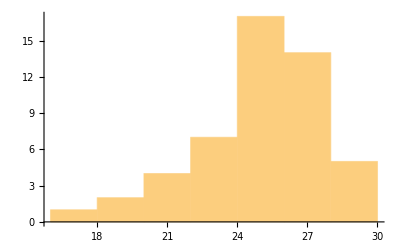

```mathematica
Histogram[%]
```

Specifically when working with large files that aren’t as simple to read with bytes, look into RecordSeparators

```mathematica
SetStreamPosition[strm,0]
```

0

Here we will attempt to find the first instance of the string “ian” in the mathematica installer:

```mathematica
FromCharacterCode[{0,0,5}]
```

.00.00.05

```mathematica
"1,2,3,45,6,5
3246853,3,56,4,3,234,5,34"
```

1,2,3,45,6,5
3246853,3,56,4,3,234,5,34

```mathematica
WriteString[file=CreateTemporary[],"1,2,3,45,6,5
3246853,3,56,4,3,234,5,34"]
```

```mathematica
file
```

/var/folders/dz/4rpzcv090x3g0_b74rbdblw40009vn/T/m000021649981

```mathematica
FilePrint[%]
```

1,2,3,45,6,5
3246853,3,56,4,3,234,5,34

```mathematica
strm1=OpenRead[file]
```

InputStream[…]

```mathematica
ReadList[strm1,Record,1,RecordSeparators->","]
```

ReadList::optx: Unknown option CharacterEncoding in ….

ReadList[InputStream[…],Record,1,RecordSeparators→,,CharacterEncoding→ASCII]

```mathematica
$CharacterEncodings
```

{AdobeStandard,ASCII,CP936,CP949,CP950,Custom,EUC-JP,EUC,IBM-850,ISO10646-1,ISO8859-10,ISO8859-11,ISO8859-13,ISO8859-14,ISO8859-15,ISO8859-16,ISO8859-1,ISO8859-2,ISO8859-3,ISO8859-4,ISO8859-5,ISO8859-6,ISO8859-7,ISO8859-8,ISO8859-9,ISOLatin1,ISOLatin2,ISOLatin3,ISOLatin4,ISOLatinCyrillic,Klingon,koi8-r,MacintoshArabic,MacintoshChineseSimplified,MacintoshChineseTraditional,MacintoshCroatian,MacintoshCyrillic,MacintoshGreek,MacintoshHebrew,MacintoshIcelandic,MacintoshKorean,MacintoshNonCyrillicSlavic,MacintoshRomanian,MacintoshRoman,MacintoshRomanPDFExport,MacintoshThai,MacintoshTurkish,MacintoshUkrainian,Math1,Math2,Math3,Math4,Math5,Mathematica1,Mathematica2,Mathematica3,Mathematica4,Mathematica5,Mathematica6,Mathematica7,PrintableASCII,ShiftJIS,Symbol,Unicode,UTF-8,UTF8,WindowsANSI,WindowsBaltic,WindowsCyrillic,WindowsEastEurope,WindowsGreek,WindowsThai,WindowsTurkish,ZapfDingbats}

```mathematica
$CharacterEncoding="WindowsThai"
```

WindowsThai

```mathematica
ReadList[strm,Record,1,RecordSeparators->{","}]
```

{lÝ.9aÿò.baå.13>£CóóÇKè:.06E÷y !xLL®@£ÚÉ.11.10E)\r.89d¶	.1a.00¿.a672.11.9d¬.b4Q.b9!"B.13.99Û}Fsï.04ê.b4×£ïÄ)QÄ.06\fö¶ö£H.8a1.93?.15d.86ë.1aWïéfÙùÁG.beï\f@waôJT.bdÖ;.aa¡?yj±3tÿ.b3.b2KËà.af.86NbXK±.0b¬2.b4çî×Ùþþj.80Å.11vF.9eÜ0.88>Áà£.sn:$(£@.9e°Q.bd¡.02ôi£9.88.b2.90w*Ù.9eÜÑ.10.994Ùm.06lía.bd~}

```mathematica
ToCharacterCode["ia¨","AdobeStandard"]
```

{105,97,168}

```mathematica
ToCharacterCode["ia¨","UTF-8"]
```

{105,97,194,168}

```mathematica
ReadList[strm,Byte,3]
```

{105,97,110}

```mathematica
FromCharacterCode[%]
```

ian

## Parallelization (the easy way)

```mathematica
ParallelTable
```

```mathematica
ParallelDo
```

```mathematica
ParallelSubmit
```

For more on this come to my next talk on High Performance Computing

```mathematica
1["dat.mx",data]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,9999972,9999987,9999988,9999989,9999990,9999991,9999992,9999993,9999994,9999995,9999996,9999997,9999998,9999999,10000000}}
 |  |  |  |

```mathematica
Get["dat.mx"]
```